```mathematica
dNdξ[ξ_,η_]:={1/4 (-1+η),(1-η)/4,(1+η)/4,1/4 (-1-η)};
dNdη[ξ_,η_]:={1/4 (-1+ξ),1/4 (-1-ξ),(1+ξ)/4,(1-ξ)/4};

computeBandJ[defPos_,ξ_,η_]:=Module[{X,Y,j11,j12,j21,j22,detJ,Jinv11,Jinv12,Jinv21,Jinv22,Jmat,Nmat,Dmat,B},

X=defPosᵀ⟦1⟧;
Y=defPosᵀ⟦2⟧;

j11 =X.dNdξ[ξ,η];
j12 =Y.dNdξ[ξ,η];
j21 =X.dNdη[ξ,η];
j22 =Y.dNdη[ξ,η];

detJ=j11 j22 - j12 j21;


Jinv11=j22 / detJ;
Jinv12 =-j12 / detJ;
Jinv21=-j21 / detJ;
Jinv22 = j11 / detJ;

Dmat={{1.0,0,0,0},{0,0,0,1.0},{0,1.0,1.0,0}};

Jmat ={{Jinv11,Jinv12,0,0},{Jinv21,Jinv22,0,0},{0,0,Jinv11,Jinv12},{0,0,Jinv21,Jinv22}};

Nmat={Riffle[dNdξ[ξ,η],{0,0,0,0}],Riffle[dNdη[ξ,η],{0,0,0,0}],Riffle[{0,0,0,0},dNdξ[ξ,η]],Riffle[{0,0,0,0},dNdη[ξ,η]]};

B=Dmat.Jmat.Nmat;

Return[{B,detJ}]
];


computeStress[σn_,Δd_,B_,Ey_,ν_,Y_]:=Module[{Δϵ,Cmat,σtr,Str,S,K,Pnp1,σnp1},

(*Compute strain increment*)
Δϵ=B.Flatten[Δd];

(*Compute an elastic trial stress*)
Cmat={{Ey/(1-ν^2),ν Ey/(1-ν^2),0},{ν Ey/(1-ν^2),Ey/(1-ν^2),0},{0,0,Ey/(2(1+ν))}};

σtr=σn+Cmat.Δϵ;

(*Compute deviatoric trial stress*)
Str = σtr-1/3(σtr⟦1⟧+σtr⟦2⟧)*{1,1,0};

(*Compute deviatoric trial stress magnitude*)
S=Sqrt[Str⟦1⟧^2+2*Str⟦3⟧^2+Str⟦2⟧^2];
(*Check for yielding*)
If[Re[S]≥ Sqrt[2/3.]Y,
(*yielding, set deviatoric stress to yield stress and add hydrostatic term*)
σnp1=Sqrt[2/3.]Y*Str/S +1/3(σtr⟦1⟧+σtr⟦2⟧)*{1,1,0};
,
(*not yielding, trial stress is new stress*)
σnp1=σtr;
];

Return[{σnp1,Δϵ}]
];


computeForce[defPos_,disp_,Ey_,ν_,Y_,σ1n_,σ2n_,σ3n_,σ4n_]:=Module[{B1,B2,σ2,B3,B4,J1,J2,J3,J4,σ1np1,σ2np1,σ3np1,σ4np1,Δϵ1,Δϵ2,Δϵ3,Δϵ4},


{B1,J1}=computeBandJ[defPos,Sqrt[1/3.],Sqrt[1/3.]];
{σ1np1,Δϵ1}=computeStress[σ1n,disp,B1,Ey,ν,Y];

{B2,J2}=computeBandJ[defPos,-Sqrt[1/3.],Sqrt[1/3.]];
{σ2np1,Δϵ2}=computeStress[σ2n,disp,B2,Ey,ν,Y];

{B3, J3}=computeBandJ[defPos,Sqrt[1/3.],-Sqrt[1/3.]];
{σ3np1,Δϵ3}=computeStress[σ3n,disp,B3,Ey,ν,Y];

{B4,J4}=computeBandJ[defPos,-Sqrt[1/3.],-Sqrt[1/3.]];
{σ4np1,Δϵ4}=computeStress[σ4n,disp,B4,Ey,ν,Y];


Return[{B1ᵀ.σ1np1 J1+B2ᵀ.σ2np1 J2+B3ᵀ.σ3np1 J3+B4ᵀ.σ4np1 J4,σ1np1,σ2np1,σ3np1,σ4np1,Δϵ1,Δϵ2,Δϵ3,Δϵ4}]

];


computeTangentStiffness[defPos_,disp_,Ey_,ν_,Y_,σ1_,σ2_,σ3_,σ4_]:=Module[{h,k},

h=1×10^-50;

k=Map[computeForce[defPos,Partition[#,2],Ey,ν,Y,σ1,σ2,σ3,σ4]⟦1⟧&,IdentityMatrix[2Length[nodes]]*I h];

Return[-Im[kᵀ]/h]

];
```

```mathematica
(*Setup problem*)
nodes={{0.0,0.0},{1.0,0.0},{1.0,1.0},{0.0,1.0}};
disp=ConstantArray[{0.0,0.0},Length[nodes]];
defPos = nodes;
Ey=200;
ν=0.29;
Y=15;
σ1n={0.,0.,0.};
σ2n={0.,0.,0.};
σ3n={0.,0.,0.};
σ4n={0.,0.,0.};
ϵ1={0.,0.,0.};
ϵ2={0.,0.,0.};
ϵ3={0.,0.,0.};
ϵ4={0.,0.,0.};

stressStrain = {{{0.,0.,0.},{0.,0.,0.}}};

(*Begin load stepping iteration*)
Do[

PrintTemporary["Load Step = ",i];

(*Apply the initial kinematic BC's*)
disp⟦3⟧+={0.001,0.0};

(*Begin Newton iteration*)
Do[

(*Calculate the total force*)
{f,σ1np1,σ2np1,σ3np1,σ4np1,Δϵ1,Δϵ2,Δϵ3,Δϵ4}=computeForce[defPos,disp,Ey,ν,Y,σ1n,σ2n,σ3n,σ4n];

(*Zero residual on boundary condition nodes, they are are supposed to have reaction forces*)
f⟦{1,2,4,5}⟧={0.0,0.0,0.0,0.0};

(*Compute residual*)
res=Norm[f];

PrintTemporary["  Residual = ",res];

(*Break if convergence achieved*)
If[res<0.001,Break[]];

(*Compute tangent stiffness*)
K =Chop[computeTangentStiffness[defPos,disp,Ey,ν,Y,σ1n,σ2n,σ3n,σ4n]];

(*Apply essential BC's to tangent stiffness*)
K⟦1⟧=Normal@SparseArray[1-> 1,2*Length[nodes]];
K⟦2⟧=Normal@SparseArray[2-> 1,2*Length[nodes]];
K⟦4⟧=Normal@SparseArray[4-> 1,2*Length[nodes]];
K⟦5⟧=Normal@SparseArray[5-> 1,2*Length[nodes]];

(*Solve the linear problem for a displacment increment*)
disp+=Partition[LinearSolve[K,f],2];

,{j,10}
];

(*Update the deformed position and stresses with the converged results*)
defPos=nodes+disp;
σ1n=σ1np1;
σ2n=σ2np1;
σ3n=σ3np1;
σ4n=σ4np1;
ϵ1+=Δϵ1;
ϵ2 +=Δϵ2;
ϵ3 +=Δϵ3;
ϵ4 +=Δϵ4;

AppendTo[stressStrain,{σ3n,ϵ3}]

,{i,50}
]
```

```mathematica
disp
```

{{-7.70265×10^-19,-1.38751×10^-18},{0.0102114,-2.46853×10^-18},{0.05,-0.0182113},{0.0426268,0.00363633}}

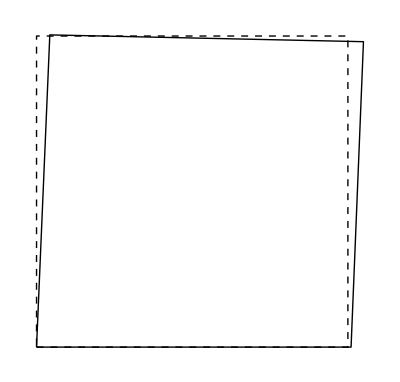

```mathematica
Graphics[{{Dashed,Line[{nodes⟦1⟧,nodes⟦2⟧,nodes⟦3⟧,nodes⟦4⟧,nodes⟦1⟧}]},{Line[{defPos⟦1⟧,defPos⟦2⟧,defPos⟦3⟧,defPos⟦4⟧,defPos⟦1⟧}]}}]
```

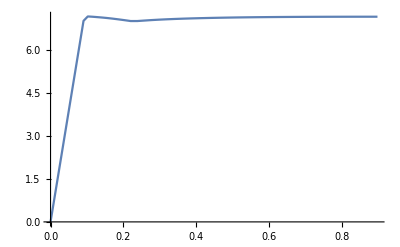

```mathematica
stress=stressStrain[[All,1]][[All,3]];
strain=stressStrain[[All,2]][[All,3]];

ListLinePlot[{strain,stress}ᵀ]
```